# Midterm

León Ocaña^1, Yordan Solórzano^2, Luis Macas^1, Juan Diego Vizcaino^1

^1Group #2, School of Physical Science and Nanotechnology, Yachay Tech University, Urcuqui - Ecuador

```mathematica
wrkdir=
"C:\\Users\\LeDar\\wrk\\dft2024\\ir-files\\results";
SetDirectory[wrkdir];
```

### Analysis of ENCUT

```mathematica
datair = Import["ecut.dat"]//Map[#/{1,1}&,#]&
```

{{250,-8.84567},{300,-8.83801},{350,-8.83681},{400,-8.83734},{450,-8.8373},{500,-8.83741},{550,-8.83765},{600,-8.83775},{650,-8.83774},{700,-8.83777},{750,-8.83779},{800,-8.83772},{850,-8.83772},{900,-8.83771}}

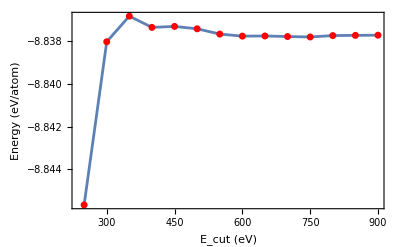

```mathematica
ListPlot[datair,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datair]}
]
```

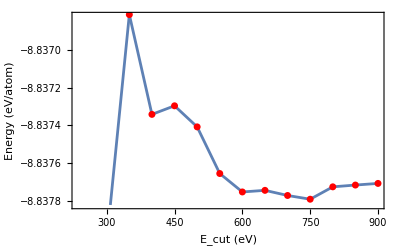

```mathematica
ListPlot[datair,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-8.83682076893569,-8.83682076893569-10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datair]}
]
```

{{400, -8.83733890452691}} point is inside of the 1 meV window. Ecut is 400eV.

### Analysis of k - points

```mathematica
datakp = Import["kps.dat"]//Map[#/{1,1}&,#]&
```

{{15,-8.83905},{16,-8.83414},{17,-8.83767},{18,-8.83723},{19,-8.83503},{20,-8.83892},{21,-8.83686},{22,-8.83625},{23,-8.83833},{24,-8.83695},{25,-8.83746},{26,-8.83766},{27,-8.8371},{28,-8.83752}}

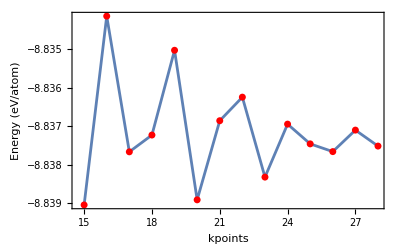

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"kpoints","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

```mathematica
{{23.985665045021904,-8.836940024060466}}
```

{{23.9857,-8.83694}}

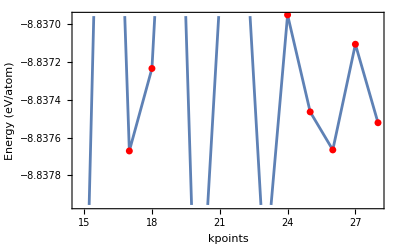

```mathematica
ListPlot[datakp,
Frame->True,
FrameLabel->{"kpoints","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Joined->True,
PlotRange->{-8.836956019695357,-8.836956019695357-10^-3},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Red,AbsolutePointSize[5],Point[datakp]}
]
```

The convergency is for 24 kpoints

For the k points grid we will use 17x17x17 to converge the energy to <1meV/atom

We know that for any crystal shape, the volume can be computed like:

```mathematica
Range[val-3,val+5,0.5]/.val->14.0//Map[(#//ToString)<>" "&,#]&//StringJoin
```

11. 11.5 12. 12.5 13. 13.5 14. 14.5 15. 15.5 16. 16.5 17. 17.5 18. 18.5 19.

```mathematica
a1 = a{1/2,1/2,0};
a2 = a{0,1/2,1/2};
a3= a{1/2,0,1/2};
a1.(a2 ×a3)
```

a^3/4

```mathematica
cell= Import["cell.dat"][[All,{1,2}]]
```

{{11.,-7.22074},{11.5,-7.75104},{12.,-8.14632},{12.5,-8.4326},{13.,-8.63067},{13.5,-8.75728},{14.,-8.82597},{14.5,-8.84773},{15.,-8.83149},{15.5,-8.78459},{16.,-8.713},{16.5,-8.62165},{17.,-8.5146},{17.5,-8.39519},{18.,-8.26621},{18.5,-8.12992},{19.,-7.98826}}

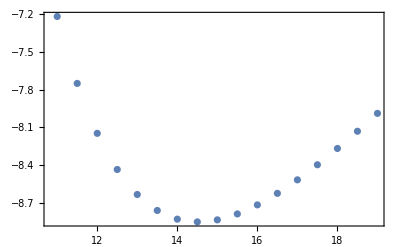

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2(6-4((v0/v)^(2/3))));
```

```mathematica
NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit::nrlnum: The function value {6.54714-0.00332106 ⅈ,7.07741-0.00320781 ⅈ,7.47267-0.00310336 ⅈ,7.75893-0.00300669 ⅈ,«4»,8.15772-0.0026135 ⅈ,8.1108-0.00254896 ⅈ,«7»} is not a list of real numbers with dimensions {17} at {e0,v0,B0,B0'} = {-0.676161,-0.415187,0.0517451,6.11089}.

FittedModel[-0.676161-0.0120847 ((6-2.22616 (-1/v)^(2/3)) (-1+«19» «1»)^2+6.11089 «1»)]

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
```

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[6.38425+4221.76/v^2-878.886/v^(4/3)-62.161/v^(2/3)]

```mathematica
nlm[v]
```

6.38425+4221.76/v^2-878.886/v^(4/3)-62.161/v^(2/3)

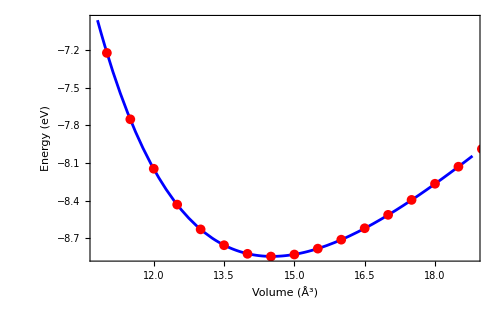

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)-0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotStyle->{AbsoluteThickness[2],Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}
]
```

```mathematica
nlm["RSquared"]
```

1.

```mathematica
opVol=FindMinimum[nlm[v],
{v,14.52}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-8.84644,{v→14.5222}}

Bulk modulus

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]]//UnitConvert[
Quantity[#,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]&(*Converting to GigaPascals as the original units are eV/Å^3*)
```

345.677 GPa

```mathematica
B0=v D[nlm[v],{v,2}]/.opVol[[2]];
B0'=-v/B0 D[v D[nlm[v],{v,2}],v]/.opVol[[2]](*Bulk Modulus pressure derivative*)
```

5.13582

```mathematica
4.260882620220651(*Adimentional*)
```

4.26088

Other way to get the mechanical properties of a crystal from the EOS.

```mathematica
nlm["BestFitParameters"]
```

{k[1]→6.38425,k[2]→-62.161,k[3]→-878.886,k[4]→4221.76}

```mathematica
Clear[B0]
```

```mathematica
sol=Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→-8.84644,B0→2.15755,v0→14.5222,B'→5.13582}}

```mathematica
Solve[v0==a0^3/4,a0]/.sol
```

{{{a0→-1.93643+3.35399 ⅈ},{a0→3.87285},{a0→-1.93643-3.35399 ⅈ}}}

```mathematica
B0comp=UnitConvert[
Quantity[2.15754898861357,("Electronvolts")/("Angstroms")^3],
"GigaPascals"]
```

345.677 GPa

### The density of states (DOS) and partial density of states (PDOS)

```mathematica
input=Import["DOSCAR","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.94385

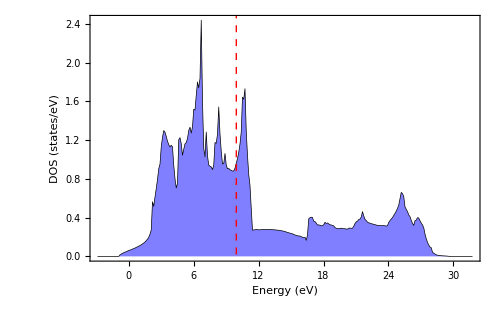

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->
Directive[Red,Dashed,
AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500]
```

Now we are going to analyze the PDOS, we have to consider this:

energy s p_y p_z p_x d_ {xy} d_ {yz} d_ {z2 - r2} d_ {xz} d_ {x2 - y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
```

```mathematica
dosall=(dos1)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

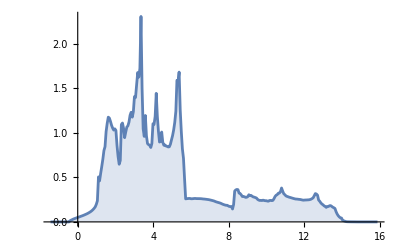

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,
#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
dosall//f[total]//
ListPlot[#,Joined->True,Filling->Axis]&
```

The s-states will be

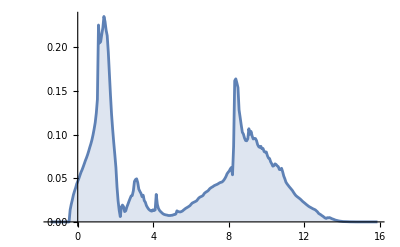

```mathematica
dosall//f[s]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For p-states

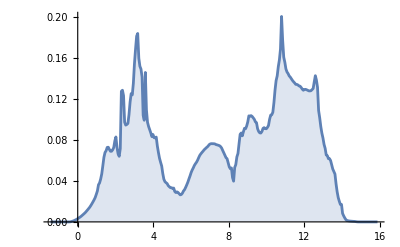

```mathematica
dosall//f[p]//
ListPlot[#,Joined->True,Filling->Axis]&
```

For d-states

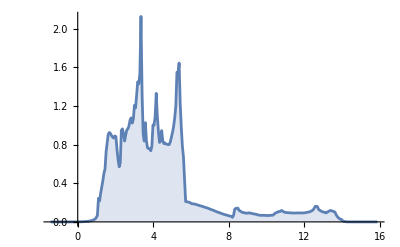

```mathematica
dosall//f[d]//
ListPlot[#,Joined->True,Filling->Axis]&
```

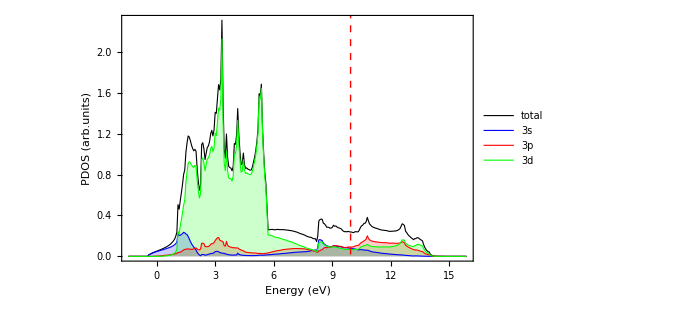

```mathematica
{dosall//f[total],dosall//f[s],dosall//f[p],dosall//f[d]}//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis, 4->Axis},
Frame->True,
FrameLabel->{"Energy (eV)","PDOS (arb.units)"},
PlotRange->All,
PlotLegends->Placed[{"total","3s","3p", "3d"},{Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->
Directive[Red, Dashed,
AbsoluteThickness[1.0]],
PlotStyle->
{{AbsoluteThickness[0.8],Black}, 
{AbsoluteThickness[0.8],Blue},
{AbsoluteThickness[0.8],Red}, 
{AbsoluteThickness[0.8],Green}},
BaseStyle->{FontFamily->"Helvetica", 
FontSize->18}
]&
```

Is the system metal, semiconductor or insulator?
The system is metallic because we observe the energy on the Fermi level is nonzero and if we do a small variation epsilon over this point, we notice not affect the energy enough to do zero or lower.

### The band structure of Ir using PROCAR_OPT file

```mathematica
(*define the Fermi elevel take from previous calculations*)
ef =input[[6,4]]
```

9.94385

```mathematica
ef=input[[6,4]];
```

```mathematica
(*This gets number of kp and bands*)
bandsinfo=Import["numbands","Table"][[1]];
{Nkpt,Nbands}=bandsinfo//{#[[4]],#[[8]]}&
```

{270,8}

```mathematica
(*This gets the high symmetry points and divisions*)
path=Import["KPOINTS-bs","Table"];
div=path[[2,1]];
```

```mathematica
(*This defines the high symmetry points labels and the length*)
hsympts=(If[(path[[5]]//Length)==4,path[[5;;-1]]//Flatten//Partition[#,4]&//#[[All,4]]&, path[[5;;-1]]//Flatten//Partition[#,5]&//#[[All,5]]&]//Drop[#,{3,Length[#],2}]&)/."GAMMA"->"Γ"
NumGridL=(hsympts//Length)-2;
```

{K,Γ,L,W,X,U,W}

```mathematica
(*This defines the band energies shifted to Ef*)
bands=Import["bandData","Table"][[2;;-1]][[All,5]]-ef//Partition[#,Nbands]&;
bandener=bands//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This defines k-point coordinates*)
kp=Import["kpts","Table"][[2;;-1]][[All,{4,5,6}]];
kpt=kp//Drop[#,{div,Nkpt-div,div}]&;
```

```mathematica
(*This liniarizes k-point coordinates in 1D*)
kpt2=Join[{0},Table[Norm[kpt[[i+1]]-kpt[[i]]],{i,(kpt//Length)-1}]]//Accumulate;
```

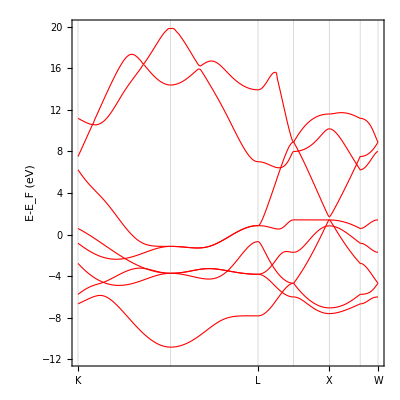

```mathematica
(*This creates the bands in kpt2 domain*)
bands2={kpt2,bandener}//Transpose;
Do[bd[i]=bands2//Map[{#[[1]],#[[2,i]]}&,#]&,{i,Nbands}];

(*please provide the bands you want to plot*)
ListPlot[Table[bd[i],{i,1,8(*Nbands*)}],
Frame->True,
FrameLabel->{"","E-E_F (eV)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->14},
Joined->True,
InterpolationOrder->2,
AspectRatio->1,
AxesStyle->Directive[Black,Dashed, AbsoluteThickness[0.7]],
FrameTicks->{{Automatic,None},{{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],hsympts}//Transpose,None}},
GridLines->{kpt2[[Join[Table[i div-(i-1),{i,0,NumGridL}],{-1}]]],None},
PlotStyle->Directive[Red,AbsoluteThickness[0.8]],
PlotRange->{{0,kpt2[[-1]]},{-12,20}}]
```

```mathematica
int5=Interpolation[bd[5]]
```

InterpolatingFunction[…]

```mathematica
FindMinimum[int5[x],x]
```

{-1.28734,{x→1.18451}}

```mathematica
e[bulk]/n-e[atom]/.{e[bulk]->-8.83752066,
e[atom]->-1.52112338,n->1}
```

-7.3164

The cohesion energy is -7.3164 eV

```mathematica
B0exp=UnitConvert[
Quantity[3.55 10^11,("Newtons")/("Meters")^2],
"GigaPascals"]
```

355. GPa

Obtaining the error for B0

```mathematica
Abs[(B0comp-B0exp)/B0exp 100]
```

2.62607

Obtaining the error for a0

{{e0→-8.84644,B0→2.15755,v0→14.5222,B'→5.13582}}

{{{a0→-1.93643+3.35399 ⅈ},{a0→3.87285},{a0→-1.93643-3.35399 ⅈ}}}

```mathematica
a0comp=3.87;
a0exp=3.84;
```

```mathematica
Abs[(a0comp-a0exp)/a0exp 100]
```

0.78125

Obtaining the error for v0

```mathematica
v0comp=14.522229230532147;
v0exp=3.84^3/4;
```

```mathematica
Abs[(v0comp-v0exp)/v0exp 100]
```

2.58872

The computed errors show a little variance regarding the experimental data.